# Testing one particular ttH@NNLO supergraph

## Resources

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/valentin/Documents/Work/Projects/alphaLoop/git_alphaLoopMisc/ltd_math_examples/example_ttbarH

```mathematica
<<"../../ltd_math_utils/ltdTools.m"
```

The documented functions in this package are: 
 ?plotGraph 
 ?findIsomorphicGraphs 
 ?constructCuts 
 ?importGraphs 
 ?getLoopLines 
 ?getCutStructure 
 ?writeMinimalJSON 
 ?contractLorentz 
 ?contractColor 
 ?extractTensCoeff 
 ?getSymCoeff 
 ?processNumerator 
 ?createSuperGraph
 ----------------------------------------- 
 Needs the package IGraphM which can be downloaded from https://github.com/szhorvat/IGraphM. !!! 
 Run: Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"] for installation.
 Make sure you have the "trace_form.log" file for the gamma-algebra

## Extracting the one ttH diagram of interest

```mathematica
(* First load all ttH  graphs *)
allTTHGraphs=importGraphs["./epem_ttH.qgr",sumIsoGraphs->False];
```

So we have many of them

```mathematica
Length[allTTHGraphs]
```

744

Many are however now the desired one, for instance:

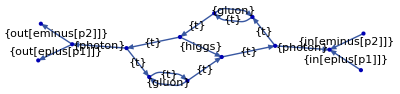

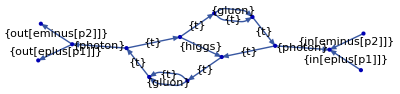

```mathematica
{plotGraph[allTTHGraphs⟦1⟧,edgeLabels->{"particleType"}],
plotGraph[allTTHGraphs⟦4⟧,edgeLabels->{"particleType"}]};
```

We can check if two diagrams are isomorphic simply with

```mathematica
findIsomorphicGraphs[allTTHGraphs⟦1;;4⟧,edgeTagging->{"particleType"}]
```

({3,2} | {}
{4,1} | {<|vertexMap→<|in(1)→in(1),v(1)→v(1),in(2)→in(2),out(1)→out(1),v(2)→v(2),out(2)→out(2),v(3)→v(3),v(4)→v(4),v(5)→v(5),v(6)→v(6),v(7)→v(7),v(8)→v(8),v(9)→v(9),v(10)→v(10)|>,permutation→Cycles[{}],orientationChange→{1,1,1,1,1,1,-1,-1,-1,-1,1,-1,1,-1,-1,1,-1}|>})

And we are only interested in one particular diagram which we will build here in order to find it in the list:

```mathematica
allTTHGraphs⟦1⟧["edges"]//InputForm
```

{in[1] -> v[1], in[2] -> v[1], v[2] -> out[1], v[2] -> out[2], v[3] -> v[1], v[4] -> v[2], v[5] -> v[3], v[3] -> v[6], v[7] -> v[4], v[4] -> v[8], v[7] -> v[5], v[9] -> v[5], v[10] -> v[6], v[6] -> v[10], 
 v[10] -> v[7], v[9] -> v[8], v[8] -> v[9]}

```mathematica
Length[allTTHGraphs⟦1⟧["edges"]]
```

17

```mathematica
allTTHGraphs⟦1⟧["particleType"]//InputForm
```

{in[eplus[p1]], in[eminus[p2]], out[eplus[p1]], out[eminus[p2]], photon, photon, t, t, t, t, higgs, t, gluon, t, t, gluon, t}

```mathematica
TargetDiagram=<|
"edges"->{
(* incoming photon *)
in[1]->v[1],in[2]->v[1],v[1]->v[3],
(* outgoing photon *)
v[4]->v[2],v[2]->out[1],v[2]->out[2],
(* top quark loop upper branch *)
v[3]->v[5],v[5]->v[6],v[6]->v[4],
(* top quark loop lower branch *)
v[4]->v[7],v[7]->v[8],v[8]->v[9],v[9]->v[10],v[10]->v[3],
(* gluons *)
v[5]->v[9],v[6]->v[8],
(* Higgs *)
v[10]->v[7]
},
"particleType"->{
in[eplus[p1]],in[eminus[p2]],photon,
photon,out[eplus[p1]],out[eminus[p2]],
t,t,t,
t,t,t,t,t,
gluon,gluon,
higgs
}
|>;
```

Now let’s find it in the list of diagrams

```mathematica
FindMyDiagram[diag_,OptionsPattern[{DEBUG->False}]]:=Block[
{diagIDsFound={}},
For[i=1,i≤Length[allTTHGraphs],++i,
If[OptionValue[DEBUG],Print["Now comparing with diag ID="<>ToString[i]];];
If[
findIsomorphicGraphs[{allTTHGraphs⟦i⟧,diag},edgeTagging->{"particleType"}]≠{},
AppendTo[diagIDsFound,i];
];
];
diagIDsFound
]
```

```mathematica
FindMyDiagram[TargetDiagram]
```

{65,72}

Check if these two diagrams are indeed the desired ones!

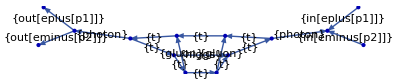

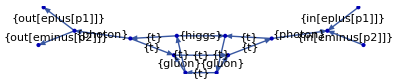

```mathematica
{plotGraph[allTTHGraphs⟦65⟧,edgeLabels->{"particleType"}],
plotGraph[allTTHGraphs⟦72⟧,edgeLabels->{"particleType"}]};
```

Yes they are!

```mathematica
allTTHGraphs⟦65⟧["edges"]
```

{in(1)→v(1),in(2)→v(1),v(2)→out(1),v(2)→out(2),v(3)→v(1),v(4)→v(2),v(5)→v(3),v(3)→v(6),v(4)→v(7),v(8)→v(4),v(7)→v(5),v(9)→v(5),v(6)→v(8),v(9)→v(6),v(7)→v(10),v(10)→v(8),v(10)→v(9)}

```mathematica
allTTHGraphs⟦65⟧["particleType"]⟦-7⟧
```

higgs

```mathematica
allTTHGraphs⟦65⟧["momentumMap"]⟦-7⟧
```

-k3

```mathematica
allTTHGraphs⟦65⟧["loopMomenta"]
```

{k1,k2,k3,k4}

```mathematica
SelectedDiagram=allTTHGraphs⟦65⟧;
```

## Extracting the one ttH diagram of interest

```mathematica
(*SelectedDiagram["numerator"]*)
```

So we can now process the numerator:

```mathematica
Print["Now performing algebra of this diagram..."];
(*processedSelectedGraph=processNumerator[SelectedDiagram,"./minFeynRulesQCDH.m",symCoefficients->False,algebraOptions->{polarizationSum->True,additionalRules->{SP[p1,p1]->0,SP[p2,p2]->0,TF->1/2,ii->I,SP[k3,k3]->mH^2}}];*)
Print["Done!"]
```

```mathematica
(*Export["processedSelectedGraph.dat",processedSelectedGraph]*)
```